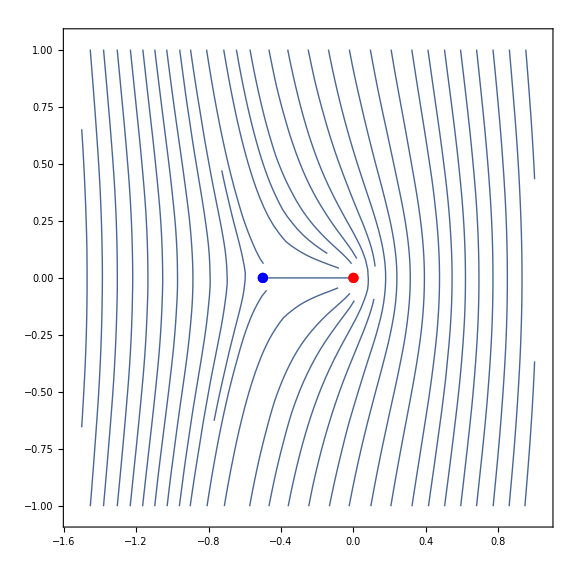
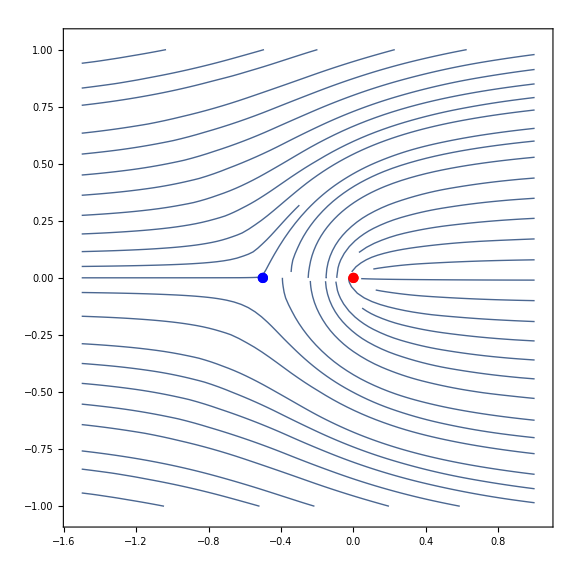

```mathematica
c=0.5;
budden=Function[x,1+c/x];
StokesGraph[budden,1]
Clear[budden,c];
```

```mathematica
BuddenF=S[r].W[(π c)/2];
%//MatrixForm
```

(ⅇ^((c π)/2) | 0
ⅇ^((c π)/2) r | ⅇ^(-(c π)/2))

```mathematica
BuddenF.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
1/%%⟦1⟧//Simplify
```

r

ⅇ^(-(c π)/2)

```mathematica
Inverse[BuddenF].J.BuddenF*.J.{1,0};
Inverse[J.BuddenF*.J].BuddenF.{1,0};
({{1, 1, Log[ρ]}, {(%%⟦1⟧+%%⟦2⟧ⅇ^(-2ⅈ ρ)), 1, (Log[ρ]+2π ⅈ)}, {(%⟦1⟧+%⟦2⟧ⅇ^(-2ⅈ ρ)), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify;
D[%,ρ]/(-2ⅈ)ⅇ^(2ⅈ ρ)//Simplify
%%-%ⅇ^(-2ⅈ ρ)//Simplify
```

0

-2 ⅈ ⅇ^(-1/2 π (c+Conjugate[c])) π (-(-1+ⅇ^(1/2 π (c+Conjugate[c])))^2+ⅇ^(π (c+Conjugate[c])) r Conjugate[r])

{{a→ⅇ^(-π (c+Conjugate[c])) (-1-ⅇ^(π Conjugate[c])+2 ⅇ^(1/2 π (c+Conjugate[c])))}}

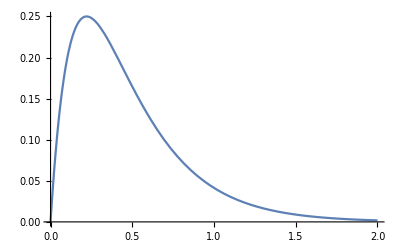

```mathematica
Solve[(-(-1+ⅇ^(1/2 π (c+Conjugate[c])))^2+ⅇ^(π (c+Conjugate[c])) r Conjugate[r])==0/.r Conjugate[r]->(1-a-ⅇ^(-c π)),a]//Simplify
Plot[a/.%,{c,0,2}]
```